-Graphics-
Image source: Lyukasóra folyóirat (see also here)

# Natural Poetry Processing

## Questions:

How well can a Machine Learning algorithm guess the Author of a Poem?

Is it relevant if the poem is written in English or in low resource (e.g. Hungarian) language?

Does it matter if it is a Translation?

How accurate this algorithm can be?

How can we measure its performance?

Where can we find an appropriate database for poems?

How to scrape it, and which features to extract?

## Definitions:

We get our textual Corpus from a homepage:

https://www.babelmatrix.org/

Our goal is to construct an aid for an Author guessing game “Lyukasóra” (“Free period” or “Cancelled class”)

https://nava.hu/talalati-lista/?q=lyukas%C3%B3ra

And to investigate its performance and how it depends on various embeddings.

## Abstraction:

First we will process Hungarian poems, which has an English translation:

See Scrpaing.nb

```mathematica
SystemOpen[NotebookDirectory[]<>"Scraping02.nb"]
```

The scraped Poems are Exported into a file, from which the data can be Imported:

```mathematica
data=ToExpression/@Import[NotebookDirectory[]<>"huenScrapedPoems.txt","List",CharacterEncoding->"UTF8"];
```

Individual entries has the following structure:

```mathematica
data[[1]]
```

<|original→<|author→Szép Ernő,lang→hu,genre→verse,title→1917-ben ,text→{Ez a kék ég vörös lehetne,,
Rajta fekete nap mehetne,
Csupa fekete fellegekbe.,
 ,
A madarak hallgathatnának,,
A nagy erdők jajgathatnának,,
Hegyek vissza jajt adhatnának.,
 ,
Gyermekek ríva ríhatnának,,
A sírok mind kinyílhatnának,,
Halottak halni híhatnának.}|>,tranlation→<|author→Mulzet, Ottilie,lang→en,genre→verse,title→1917,text→{This blue sky scarlet could be,,
On it black sun’s trajectory,,
Into black clouds then proceeds.,
 ,
The birds could all silent be,,
The great forests lament mournfully,,
The mountains could give back the scream.,
 ,
Children’s cries whining heard,,
All the graves could open wide,,
The dead believing they could die. }|>|>

```mathematica
data[[1]]//Dataset
```

## Computation:

### Basic Statistics:

```mathematica
Reverse[SortBy[Tally[#["original"]["author"]&/@data],Last]]
PieChart[Association@@(Rule@@#&/@%),ChartLabels->{Invisible/@First/@%},LabelingFunction->(Placed[#3[[2,1]][[1]],Tooltip]&)]
```

{{Pilinszky János,938},{Ady Endre,789},{József Attila,674},{Fodor Ákos,600},{Radnóti Miklós,564},{Sebestyén Péter,440},{Weöres Sándor,436},{Pintér Tibor,330},{Nemes Nagy Ágnes,297},{Kosztolányi Dezső,275},{Petőfi Sándor,260},{Benő Attila,250},{Baka István,200},{Beney Zsuzsa,189},{Kányádi Sándor,180},{Arany János,176},{Juhász Gyula,167},{Szép Ernő,159},{Babits Mihály,147},{Mezei András,140},{Ladányi Mihály,130},{Faludy György,130},{Kiss Judit Ágnes,110},{Petri György,109},{Orbán Ottó,100},{Illyés Gyula,100},{Gyukics Gábor,100},{Balassi Bálint,100},{Vörösmarty Mihály,99},{Csokonai Vitéz Mihály,99},{Szabó Lőrinc,90},{Tóth Krisztina,89},{Szilágyi Domokos,80},{Reményik Sándor,80},{Rafi Lajos,80},{Károlyi Amy,80},{Csoóri Sándor,80},{Demény Ottó,79},{Röhrig Géza,70},{Kemény István,70},{Balla Zsófia,68},{Rab Zsuzsa,60},{Kassák Lajos,60},{Hárs Ernő,60},{Székely Magda,59},{Tóth Imre,50},{Tóth Árpád,50},{Tandori Dezső,50},{Örkény István,50},{Kukorelly Endre,50},{Karinthy Frigyes,50},{Heltai Jenő,50},{Berzsenyi Dániel,50},{Bella István,50},{Vas István,40},{Reviczky Gyula,40},{Rakovszky Zsuzsa,40},{Petrőczi Éva,40},{Petőcz András,40},{Nagy László,40},{Kántor Péter,40},{Kálnoky László,40},{Gergely Tamás,40},{Füst Milán,40},{Ferencz Győző,40},{Borbély Szilárd,40},{Bari Károly,40},{Áprily Lajos,40},{Acsai Roland,40},{Vajda János,39},{Váci Mihály,39},{Utassy József,30},{Tamkó Sirató Károly,30},{Rónay György,30},{Pásztor Béla,30},{Páskándi Géza,30},{Móricz Zsigmond,30},{Kölcsey Ferenc,30},{Jékely Zoltán,30},{G. István László,30},{Gergely Ágnes,30},{Esterházy Péter,30},{Eörsi István,30},{Emőd Tamás,30},{Birtalan Balázs,30},{Szenes Anikó,29},{Kaffka Margit,29},{Bartók Béla,29},{Varró Dániel,20},{Tóth Judit (Judit Guillaume),20},{Tompa Mihály,20},{Szabédi László,20},{Spiró György,20},{Somlyó György,20},{Sík Sándor,20},{Rejtő Jenő,20},{Nyelvemlékek,20},{Márai Sándor,20},{Lázár Ervin,20},{Kovács András Ferenc,20},{Kormos István,20},{Konrád György,20},{Kisfaludy Sándor,20},{Kisfaludy Károly,20},{Hajnal Anna,20},{Győrffy Ákos ,20},{Grecsó Krisztián,20},{Faludi Ferenc,20},{Dsida Jenő,20},{Dragomán György,20},{Csukás, István,20},{Cseke Gábor,20},{Batsányi János,20},{Baranyi Ferenc,20},{Zrínyi Miklós,10},{Zalán Tibor,10},{Tinódi Lantos Sebestyén,10},{Szvoren Edina,10},{Szilágyi György,10},{Szabó Magda,10},{Somlyó Zoltán,10},{Ratkó József,10},{Rába György,10},{Podolszki  József,10},{Parti Nagy Lajos,10},{Pap Károly,10},{Ország-Land, Thomas,10},{N. Ullrich Katalin,10},{Nagypál István,10},{Nádas Péter,10},{Mezey Katalin,10},{Mészöly Miklós,10},{Mándy Iván,10},{Madách Imre,10},{Lévay József,10},{Krúdy Gyula,10},{Kornis Mihály,10},{Kiss József,10},{Kalász Orsolya,10},{Juhász Ferenc,10},{Jókai Anna,10},{Jász Attila,10},{Horváth Elemér,10},{Hervay Gizella,10},{Határ Győző,10},{Hamvas Béla,10},{Gárdonyi Géza,10},{Garay János,10},{Garai Gábor,10},{Fésűs Éva,10},{Fejes Endre,10},{Erdős Virág,10},{Erdély, Miklós,10},{Eötvös József,10},{Devecseri Gábor,10},{Déry Tibor,10},{Darvasi László,10},{Dalos, György,10},{Csanádi Imre,10},{Choli Daróczi, József,10},{Bornemisza Péter,10},{Benjámin László,10},{Bene Zoltán,10},{Balázs F. Attila,10},{Balázs Béla,10}}

-Graphics-

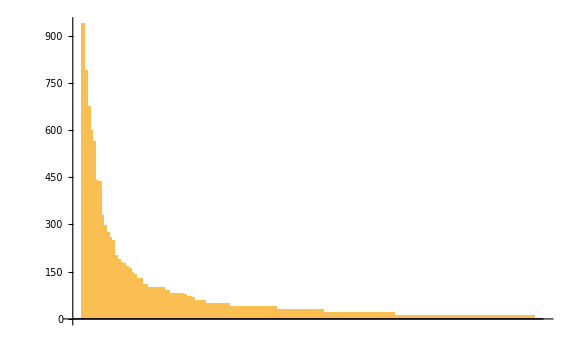

```mathematica
BarChart[Last/@Reverse[SortBy[Tally[#["original"]["author"]&/@data],Last]]]
```

```mathematica
autorList=First/@Reverse[SortBy[Tally[#["original"]["author"]&/@data],Last]];
```

### FreePeriod (Lyukasóra) simulator:

```mathematica
freePeriod[corpus_]:=Module[
{salt,randomPoem},
salt=StringJoin[RandomChoice[Join[#,ToUpperCase[#]]&@Alphabet[],4]];
randomPoem=RandomChoice[data];
Print[randomPoem["original"]["text"]//StringJoin];
Print[Hash[{randomPoem["original"]["author"],salt},"SHA","Base36String"]];
Button["Show the Author",Print[randomPoem["original"]["author"]];Print[salt]]
]
```

```mathematica
freePeriod[data]
```

Lement a nap. De nem. Még látható.Csak  voltaképpen  ment le, még az égbolttenyéröblében tartja ezt a másik,megtévesztésig hasonló napot,akár egy homokóra felsőüvegcsészéjét, melyből már kipergetta voltaképpeni.És lent a lámpák csattogásaia drótkötélen imbolyogva,a huzalok e természeti hangja,mit nem vezérel más, csupán a szél.Ezek már más beszédek,ezek az önmaguk mögélecsúszó helyettesitések,a vissza-vissza integettetések,ezekkel már sietni kell1969-1979

4w8osvunrxl3uho26rxbnqy5prccx28

Show the Author

Nemes Nagy Ágnes

DKDD

### Classifier:

We randomly select a training set containing 2000 poems:

```mathematica
trainingIndex=RandomSample[Range[Length[data]],2000];
trainingSet=StringJoin[#["original"]["text"]]->#["original"]["author"]&/@data[[trainingIndex]];
```

And use a Classifier with all Automatic Options:

```mathematica
c=Classify[trainingSet]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Text
Number of classes | 150
Accuracy | (75.53.0) %
Method | Markov
Single evaluation time | 6.09 ms/example
Batch evaluation speed | 406. examples/s
Loss | 38.1 ± 14.
Model memory | 44.7 MB
Training examples used | 2000 examples
Training time | 5.29 s
 |

### Measuring the performance:

```mathematica
(*Author - PredictedAuthor Pairs*)
aaPairs=Monitor[Table[{#["original"]["author"],c[StringJoin[#["original"]["text"]]]}&@data[[Complement[Range[Length[data]],trainingIndex]]][[i]],{i,1,Length[data]-Length[trainingIndex]}],{i,Length[data]-Length[trainingIndex]}];
```

```mathematica
dict=Association@@Table[autorList[[i]]->i,{i,1,Length[autorList]}];
```

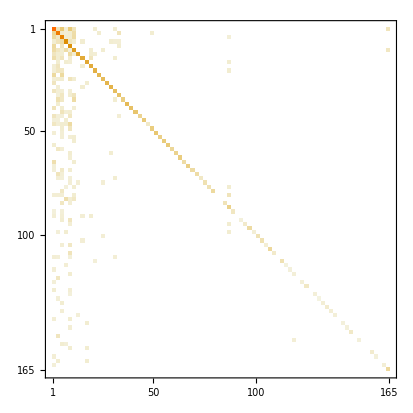

```mathematica
MatrixPlot[confusionMatrix=SparseArray[Rule@@#&/@(Tally[aaPairs]/.{a_String,b_String}:>{dict[a],dict[b]})(*/.{l_List,n_}:>l->n*)]]
```

How many times we guess correctly? (How Accurate is the model?)

```mathematica
Tr[confusionMatrix]/Total[Flatten[confusionMatrix]]//N
```

0.729668

Precision:

```mathematica
testSet=StringJoin[#["original"]["text"]]->#["original"]["author"]&/@data[[Complement[Range[Length[data]],trainingIndex]]];
Mean[Values[ClassifierMeasurements[c,testSet[[;;]],"Precision"]]/.Indeterminate->Nothing[]]
```

0.924583

Recall:

```mathematica
Mean[Values[ClassifierMeasurements[c,testSet[[;;]],"Recall"]]/.Indeterminate->Nothing[]]
```

0.564141

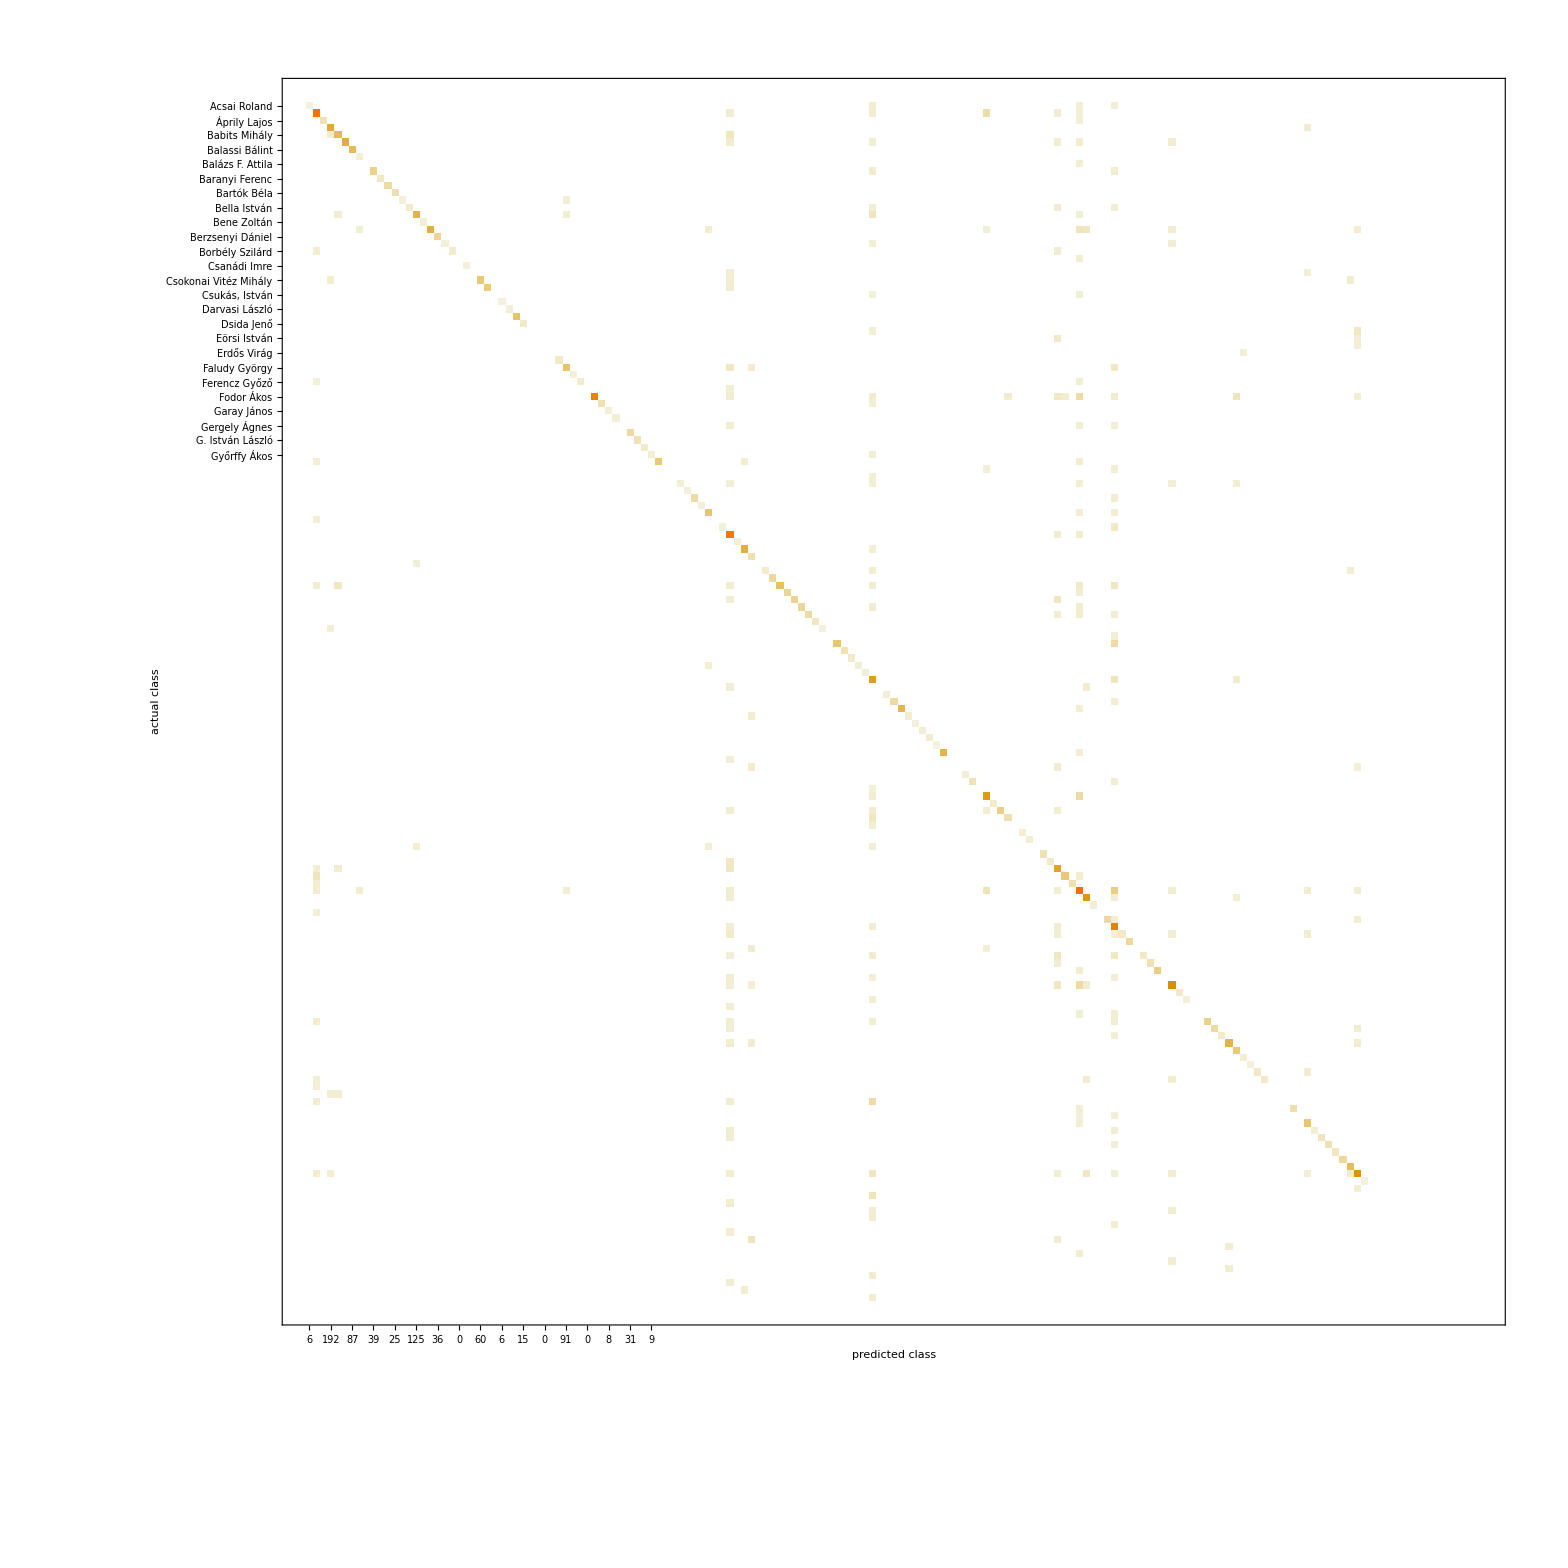
Classifier Measurements
Classifier method | Markov
Number of test examples | 10058
Accuracy | (73.00.4) %
Accuracy baseline | (7.910.27) %
Single evaluation time | 7.97 ms/example
Batch evaluation speed | 694. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[c,testSet[[;;]],"Report"]
```

### Author Networks:

```mathematica
Manipulate[
Graph[
AdjacencyGraph[
Map[If[#>p,1,0]&,((confusionMatrix/Total[Flatten[confusionMatrix]])),{2}]
],
VertexLabels->Table[i->Placed[autorList[[i]],Tooltip],{i,1,Length[autorList]}]],
{p,0,0.005}]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[confusionMatrix].

AdjacencyGraph::matsq: Argument confusionMatrix at position 2 is not a non-empty square matrix.

```mathematica
Manipulate[
Graph[AdjacencyGraph[Map[If[#>p,1,0]&,(If[Total[#]==0,0 #,#/Total[1.#]]&/@(confusionMatrix)),{2}]],VertexLabels->Table[i->Placed[autorList[[i]],Tooltip],{i,1,Length[autorList]}]],
{{p,0.5},0,0.5}]
```

AdjacencyGraph::matsq: Argument confusionMatrix at position 2 is not a non-empty square matrix.

```mathematica
(*Athor - First 3 Author Guess with biggest probabilities*)
aaGuesses=Monitor[
Table[
{
#["original"]["author"],First/@c[StringJoin[#["original"]["text"]],{"TopProbabilities",3}]
}&@data[[Complement[Range[Length[data]],trainingIndex]]][[i]],
{i,1,Length[data]-Length[trainingIndex]}
],
{i,Length[data]-Length[trainingIndex]}]
```

{{Faludy György,{József Attila,Radnóti Miklós,Faludy György}},{Pilinszky János,{Pilinszky János,Sebestyén Péter,József Attila}},{Fodor Ákos,{Fodor Ákos,Petőfi Sándor,József Attila}},{Radnóti Miklós,{Radnóti Miklós,József Attila,Weöres Sándor}},10050,{Orbán Ottó,{József Attila,Radnóti Miklós,Pilinszky János}},{Pilinszky János,{Pilinszky János,Kosztolányi Dezső,Weöres Sándor}},{Kosztolányi Dezső,{Kosztolányi Dezső,Ady Endre,József Attila}},{Pilinszky János,{Pilinszky János,József Attila,Radnóti Miklós}}}
 |  |  |  |

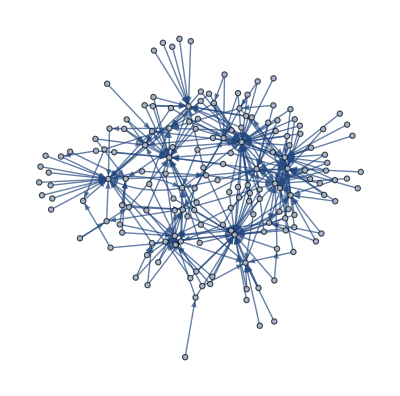

```mathematica
G=SimpleGraph[Flatten[Table[Thread[GroupBy[aaGuesses,First][[i]][[1,1]]->First/@SortBy[Tally[Flatten[#[[2]]&/@GroupBy[aaGuesses,First][[i]]]],#[[2]]&][[;;UpTo[2]]]],{i,1,Length[GroupBy[aaGuesses,First]]}]],VertexLabels->Placed[Automatic,Tooltip]]
```

```mathematica
CommunityGraphPlot[G]
```

-Graphics-

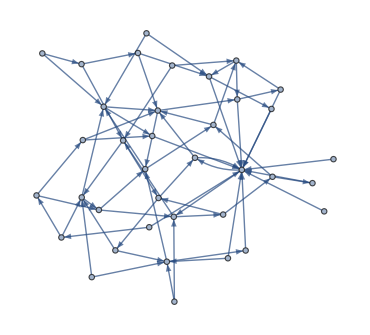

```mathematica
VertexDelete[G,_?(VertexInDegree[G,#]==0&)]
```

### Enhanced FreePeriod (Lyukasóra) simulator:

```mathematica
freePeriod2[corpus_]:=Module[
{salt,randomPoem},
salt=StringJoin[RandomChoice[Join[#,ToUpperCase[#]]&@Alphabet[],4]];
randomPoem=RandomChoice[data];
Print[randomPoem["original"]["text"]//StringJoin];
Print[Hash[{randomPoem["original"]["author"],salt},"SHA","Base36String"]];
{
Button["Show Classificator Guess",Print[c[StringJoin[randomPoem["original"]["text"]]]];],
Button["Show the Author",Print[randomPoem["original"]["author"]];Print[salt]]
}
]
```

```mathematica
freePeriod2[data]
```

üres az istálló s a jászol
  idén se lesz nálunk karácsony
  hiába vártok
  nem jönnek a három királyok 

  Sok dolga van a teremtőnek
  mindenkivel ő sem törődhet
  messzi a csillag
  mindenüvé nem világíthat 
  megértjük persze mit tehetnénk
  de olyan sötétek az esték
  s a szeretetnek
  hiánya nagyon dideregtet 
  előrelátó vagy de mégis
  nézz uram a hátad mögé is
  ott is lakoznak
  s örülnének a mosolyodnak

qe6tty9stqv3cw3jr49x1qxliylsbc4

{Show Classificator Guess,Show the Author}

Ady Endre

Kányádi Sándor

sNGg

### Word Clouds and some pre processing:

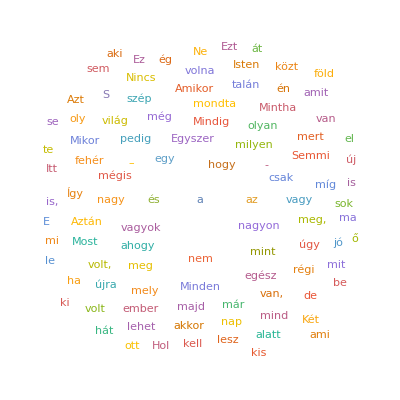

```mathematica
WordCloud[Flatten[Table[Flatten[StringSplit/@data[[i]]["original"]["text"]],{i,1,Length[data]}]]]
```

Hungarian Stop-words:
https://github.com/stopwords-iso/stopwords-hu

```mathematica
huStop=Import["https://raw.githubusercontent.com/stopwords-iso/stopwords-hu/master/stopwords-hu.txt","List",CharacterEncoding->"UTF8"];
```

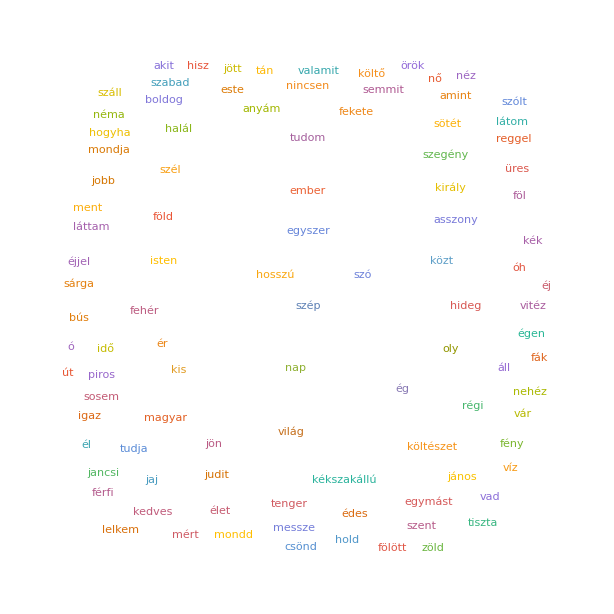

```mathematica
WordCloud[DeleteCases[Flatten[Table[Flatten[StringDelete[#,PunctuationCharacter]&/@StringSplit/@ToLowerCase/@ data[[i]]["original"]["text"]],{i,1,Length[data]}]],_?(MemberQ[huStop,#]&)]]
```

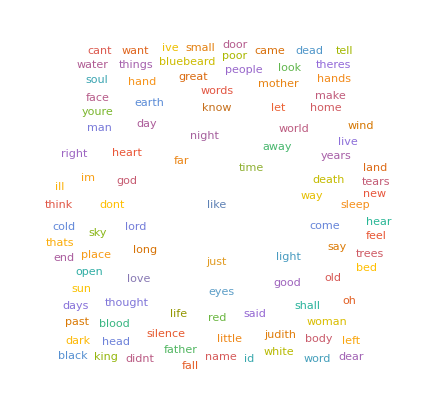

```mathematica
WordCloud[DeleteStopwords[Flatten[Table[Flatten[StringDelete[#,PunctuationCharacter]&/@StringSplit/@ToLowerCase/@ data[[i]]["tranlation"]["text"]],{i,1,Length[data]}]]]]
```

### Different embeddings:

#### Lost in Translation:

```mathematica
engTrainingSet=StringJoin[#["tranlation"]["text"]]->#["original"]["author"]&/@data[[trainingIndex]];
engTestSet=StringJoin[#["tranlation"]["text"]]->#["original"]["author"]&/@data[[Complement[Range[Length[data]],trainingIndex]]];
```

```mathematica
engc=Classify[engTrainingSet]
```

ClassifierFunction[…]

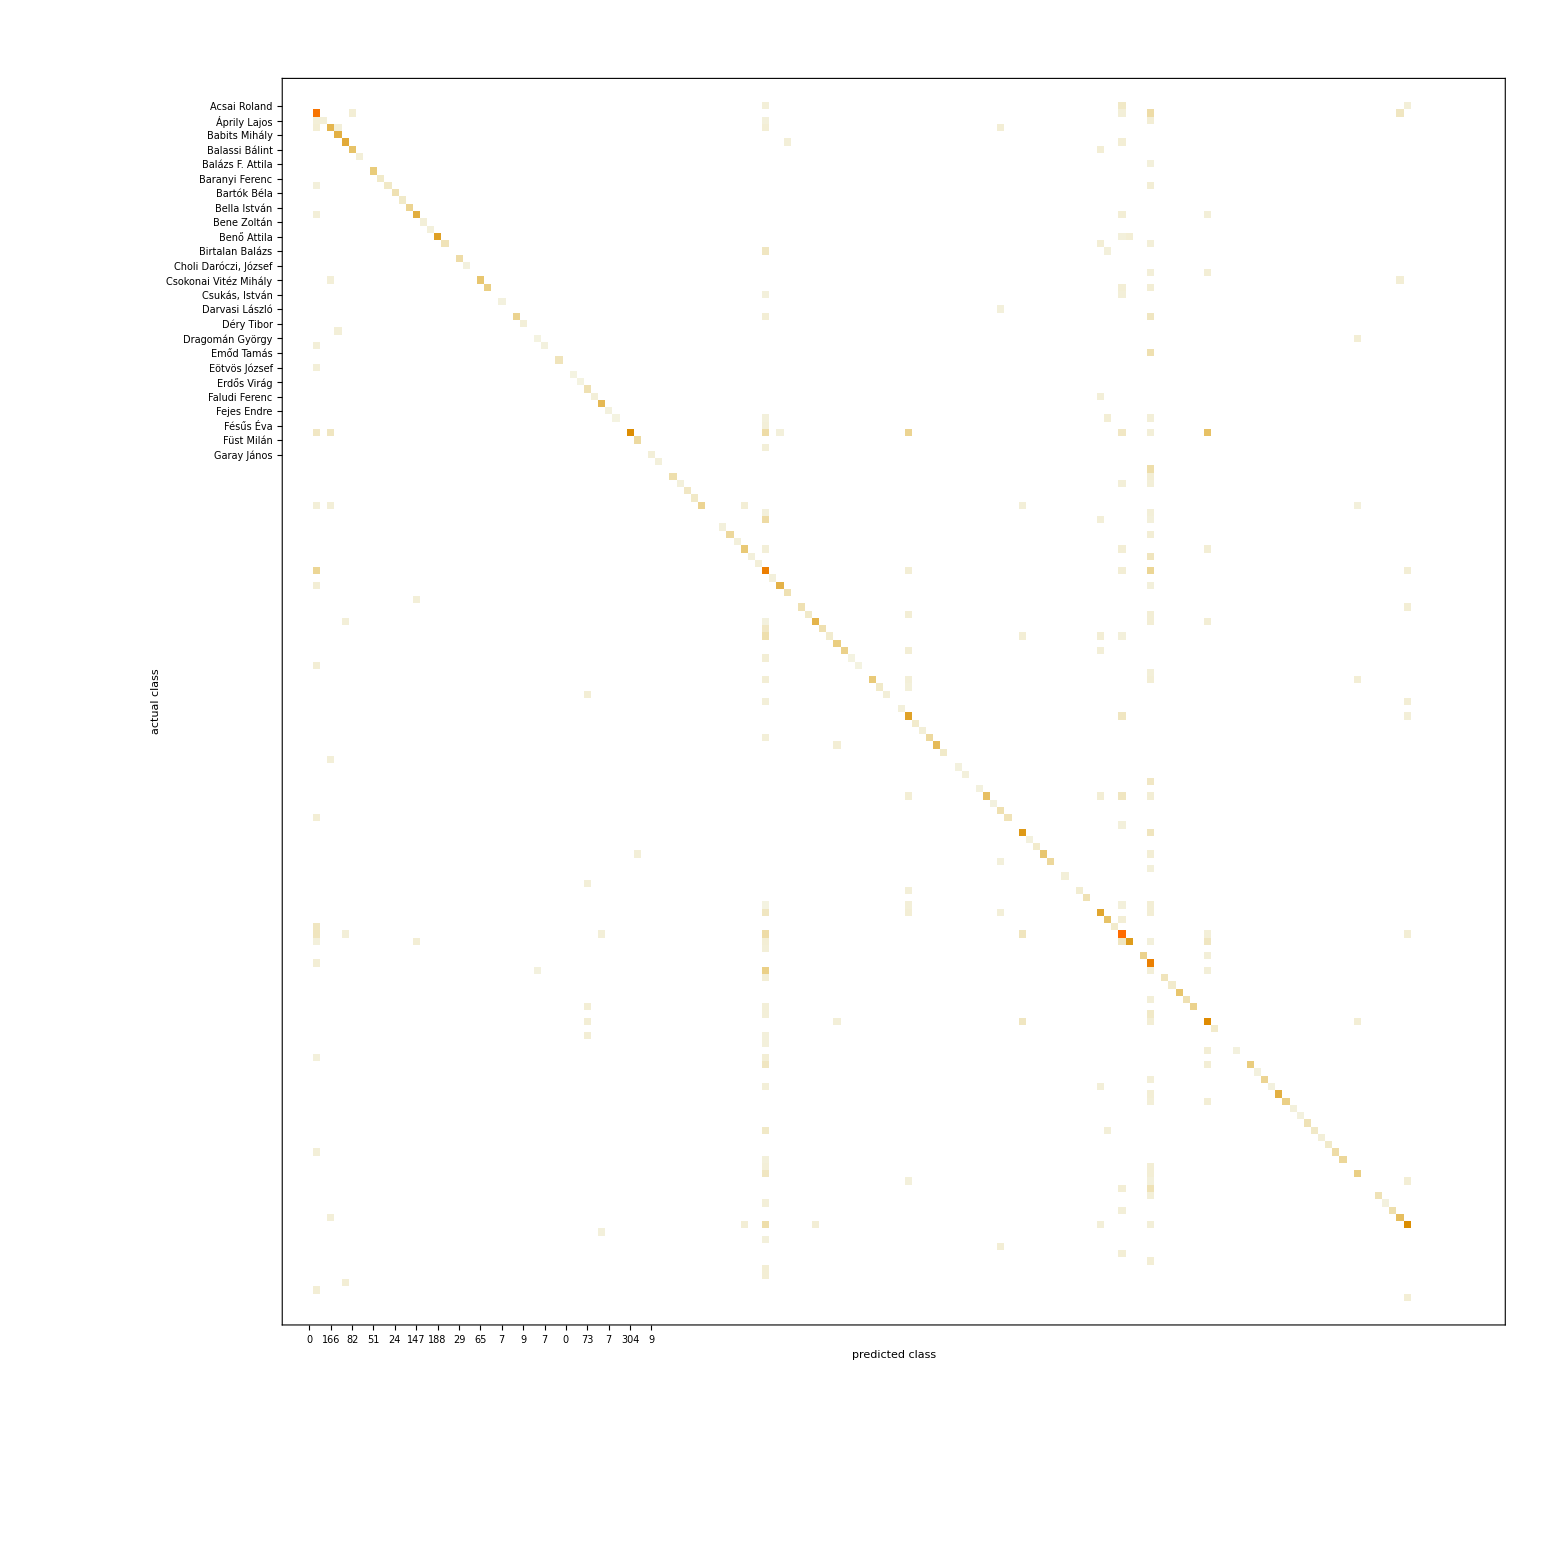
Classifier Measurements
Classifier method | Markov
Number of test examples | 10058
Accuracy | (74.30.4) %
Accuracy baseline | (7.860.27) %
Single evaluation time | 10.5 ms/example
Batch evaluation speed | 584. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[engc,engTestSet[[;;]],"Report"]
```

#### Bag of words

```mathematica
embedding[str_]:=Sort[StringSplit[StringDelete[ToLowerCase[str],PunctuationCharacter]]]
```

```mathematica
bwTrainingSet=embedding[StringJoin[#["tranlation"]["text"]]]->#["original"]["author"]&/@data[[trainingIndex]];
bwTestSet=embedding[StringJoin[#["tranlation"]["text"]]]->#["original"]["author"]&/@data[[Complement[Range[Length[data]],trainingIndex]]];
```

```mathematica
bwTrainingSet[[1]]
```

{across,age,always,and,and,and,at,blond,blood,bodies,by,cannon,childhood,combat,cooling,daybreak,dovewhite,dragged,drizzle,each,each,each,emerged,emerged,far,ferocious,flags,from,grey,have,he,heavy,helmets,his,how,i,in,in,is,kneedeep,kneeling,last,leaning,lips,loneliness,lovers,male,meadow,muddy,never,odours,of,oh,oh,old,passed,past,peachripe,poet,proceeding,protecting,reach,seedling,shrubs,sings,sizzling,skulls,slippery,soldiers,song,stands,steaming,strong,the,the,the,the,the,their,their,their,to,today,two,urgent,walked,wheels,will,with,with,with,yesterday,you,you}→Radnóti Miklós

```mathematica
bwc=Classify[bwTrainingSet]
```

ClassifierFunction[…]

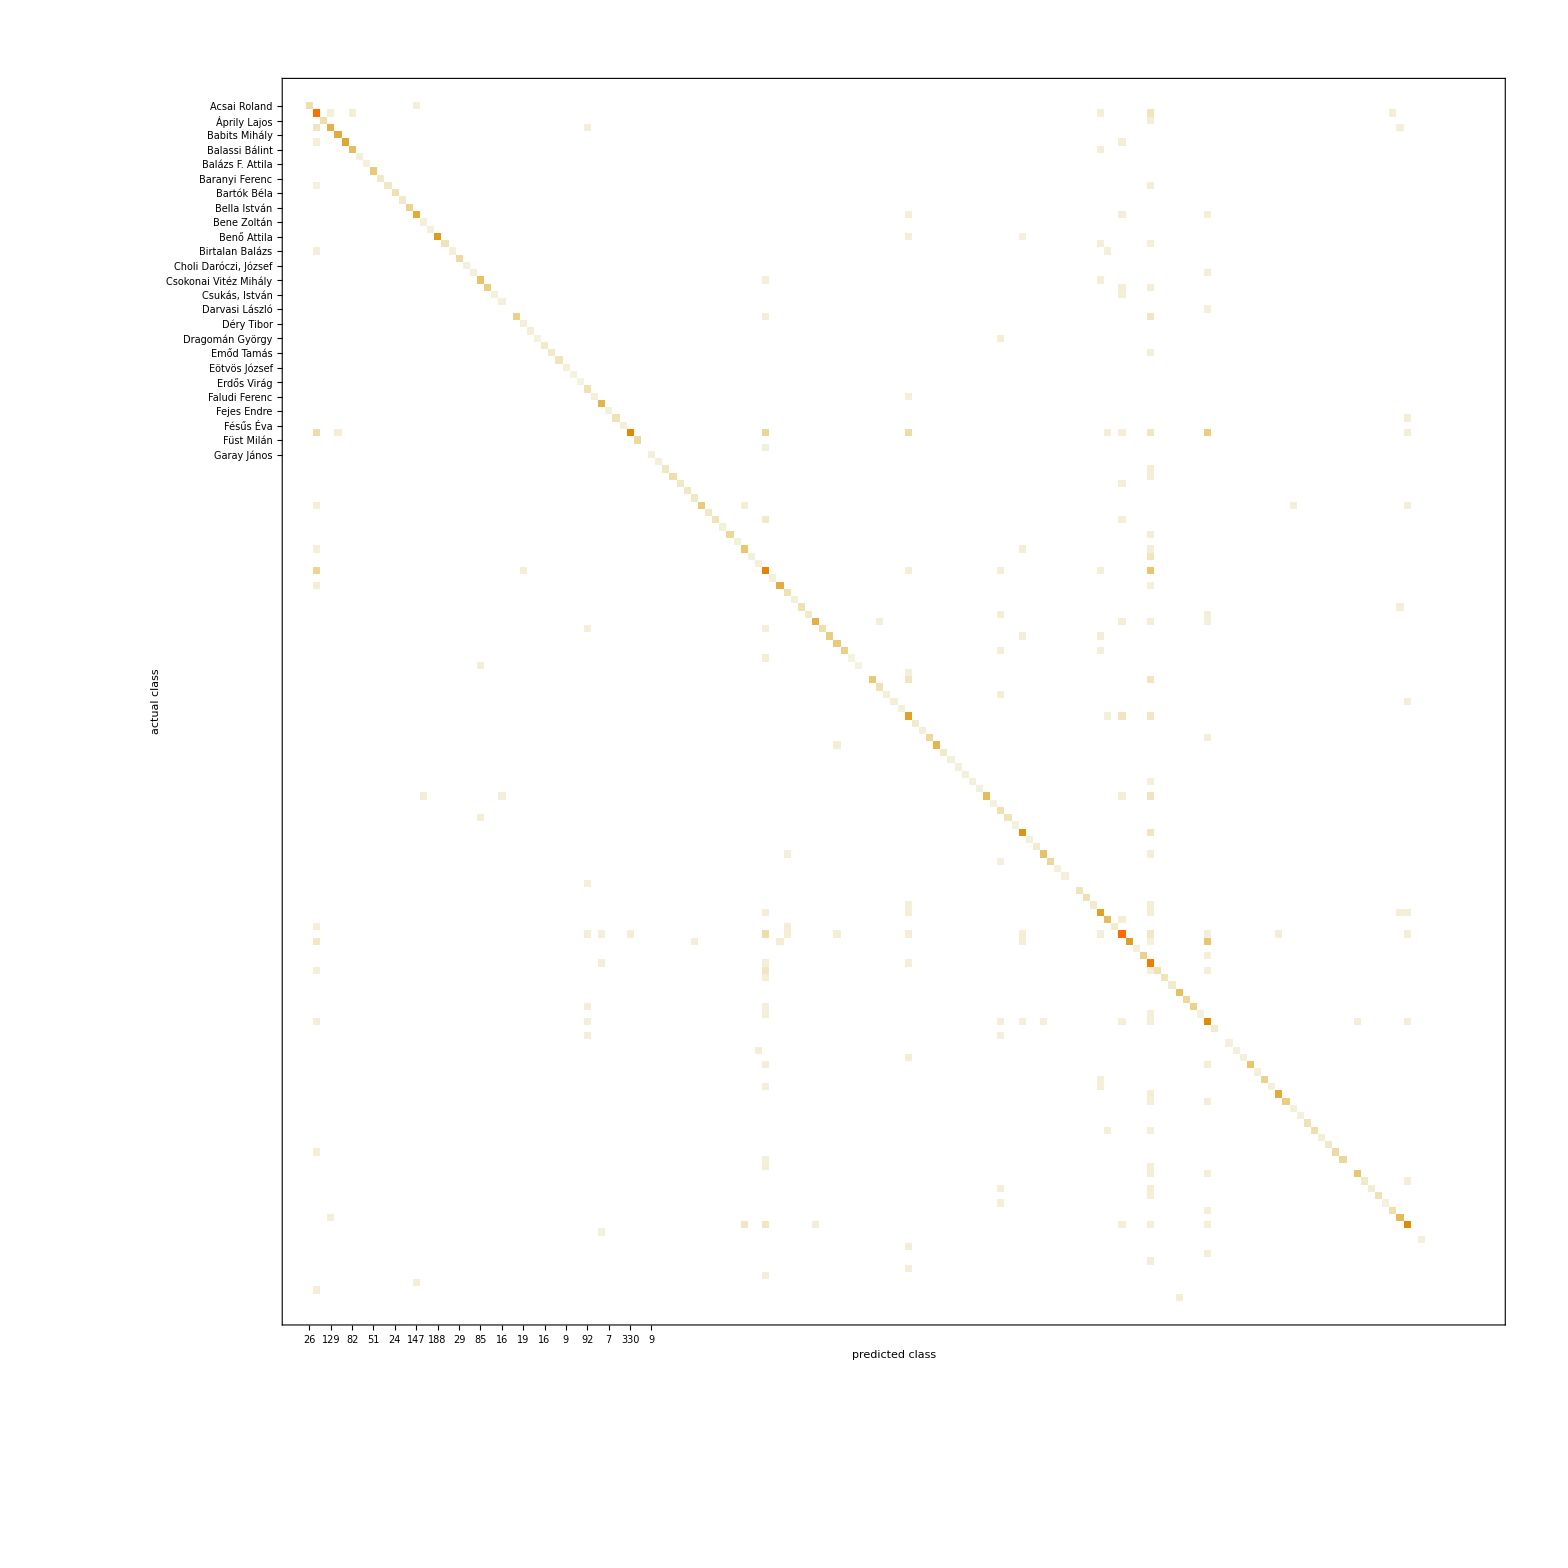
Classifier Measurements
Classifier method | Markov
Number of test examples | 10058
Accuracy | (77.30.4) %
Accuracy baseline | (7.860.27) %
Single evaluation time | 8. ms/example
Batch evaluation speed | 961. examples/s
-Graphics- |

```mathematica
ClassifierMeasurements[bwc,bwTestSet[[;;]],"Report"]
```

#### Most frequent words:

```mathematica
embedding[str_]:=First/@Reverse[SortBy[Tally[StringSplit[StringDelete[ToLowerCase[str],PunctuationCharacter]]],Last]][[;;UpTo[15]]]
```

```mathematica
bwTrainingSet=embedding[StringJoin[#["tranlation"]["text"]]]->#["original"]["author"]&/@data[[trainingIndex]];
bwTestSet=embedding[StringJoin[#["tranlation"]["text"]]]->#["original"]["author"]&/@data[[Complement[Range[Length[data]],trainingIndex]]];
```

```mathematica
bwTrainingSet[[1]]
```

{a,and,i,my,the,like,im,to,of,in,why,on,life,ive,it}→Kassák Lajos

```mathematica
bwc=Classify[bwTrainingSet]
```

ClassifierFunction[…]

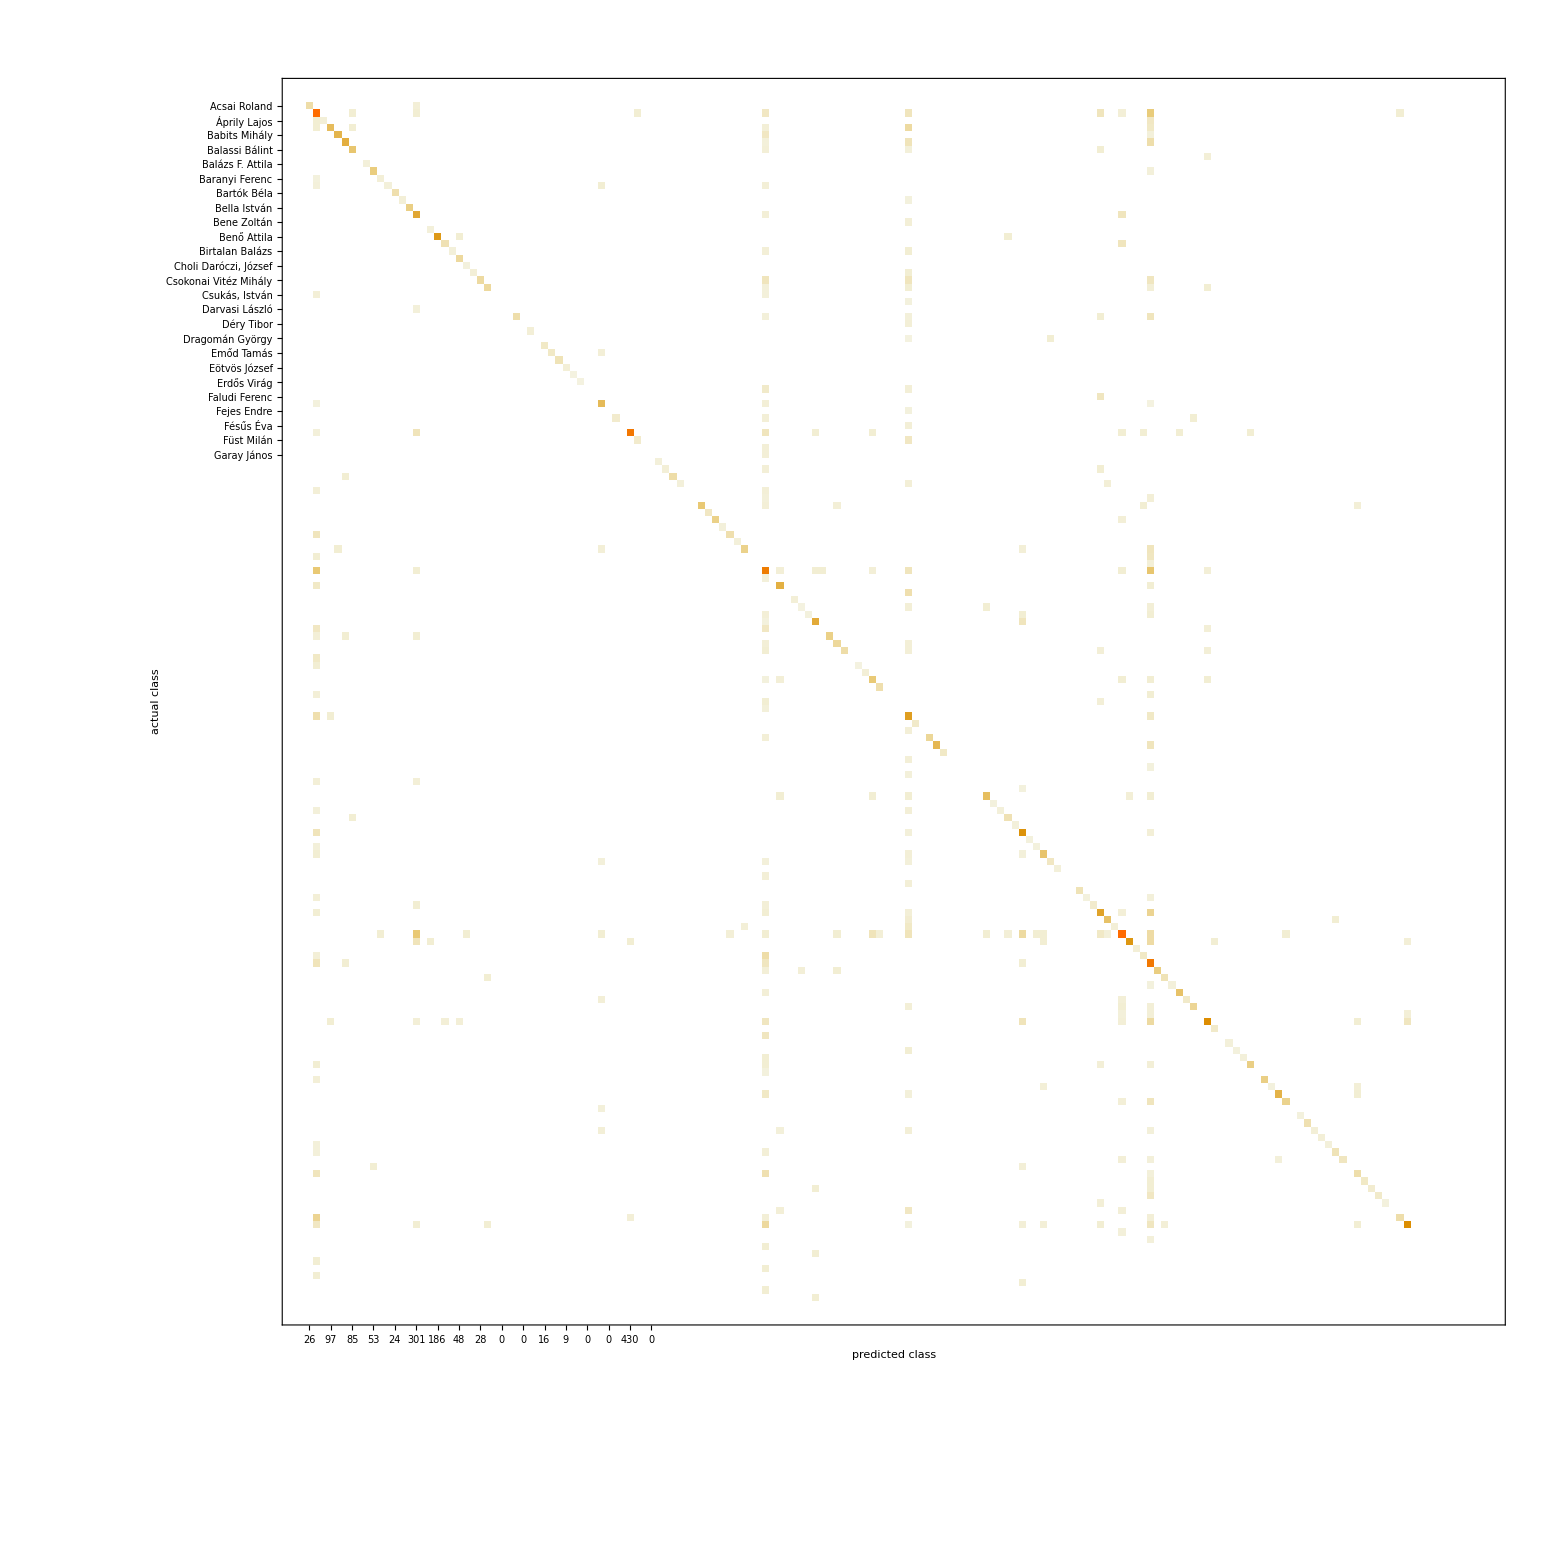
Classifier Measurements
Classifier method | Markov
Number of test examples | 10058
Accuracy | (63.10.5) %
Accuracy baseline | (7.860.27) %
Single evaluation time | 5.43 ms/example
Batch evaluation speed | 10. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[bwc,bwTestSet[[;;]],"Report"]
```

## Interpretation:

We were able to Scrape a relatively big, rich and clean corpus of Poems (which contain low resource languages e.g. Hungarian, and their translations for example to English)

Based on only 2000 Poems (16 % of the corpus) we could train a relatively accurate Poem Classifier:

Accuracy ~ 73 %

Mean Precision ~ 92 %

Mean Recall ~ 55 %

The results are supricingly robust in the change of embedding:

They are stable under (English) translation

Beg of words Embedding

## Questions II:

How semantic analysis could help on the performance?

How could we use Neural Networks?

### Neural Net for semantic word representation

https://resources.wolframcloud.com/NeuralNetRepository/resources/BERT-Trained-on-BookCorpus-and-Wikipedia-Data/

```mathematica
net=NetModel["BERT Trained on BookCorpus and Wikipedia Data"]
```

NetChain[<>]

```mathematica
net["and I go here"]//Dimensions
```

{6,768}

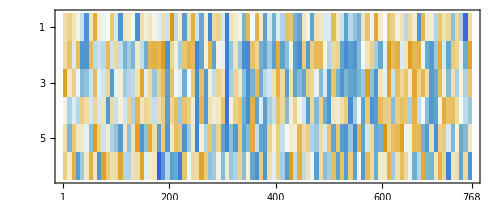

```mathematica
MatrixPlot[net["and I go here"]]
```

## Further References and Resources:

Classification:

https://www.wolfram.com/language/introduction-machine-learning/classification/

Scraping example in Wolfram Language:

https://www.wolfram.com/broadcast/video.php?c=105&p=8&v=3081

Transformer Neural Nets

https://www.wolfram.com/language/12/neural-network-framework/use-transformer-neural-nets.html

https://resources.wolframcloud.com/NeuralNetRepository/resources/BERT-Trained-on-BookCorpus-and-Wikipedia-Data/

Lyukasóra (Hungarian):

https://nava.hu/talalati-lista/?q=lyukas%C3%B3ra

Natural Language Processing

https://www.youtube.com/watch?v=otH29Uoo-HE

https://www.cl.cam.ac.uk/teaching/1920/NLP/materials.html

https://www.cl.cam.ac.uk/teaching/2122/MLRD/materials.html

https://www.youtube.com/playlist?list=PLoROMvodv4rOFZnDyrlW3-nI7tMLtmiJZ

https://web.stanford.edu/class/cs224n/